```mathematica
param={ρ->20,d->1,σoff->0.1,σon->4.5,τ->0.8};
Binsn=36;
Binsm=40;
x1=ρ*u1/d;
r=1-x1+(σoff+σon)/d;
θ=Sqrt[(x1-(σoff+σon)/d)^2+4*σon*x1/d];
v1=d*(r+θ-1)/2;
v2=d*(r-θ-1)/2;
```

```mathematica
(*Taylor expansion of (v1 ⅇ^(-v2 τ)- v2 ⅇ^(-v1 τ))/(d θ)*)
G1n=(v1*Exp[-v2*τ]-v2*Exp[-v1*τ])/(d*θ)/.param;
v1n=Table[0,{i,1,Binsn}];
v1n[[1]]=Series[G1n,{u1,-1,Binsn}];
For[i=2,i<=Binsn,i++,v1n[[i]]=SeriesCoefficient[v1n[[1]],{u1,-1,i-1}]];
v1n[[1]]=G1n/.param/.u1->-1;
```

```mathematica
(*Taylor expansion of M[σon/d,(σoff+σon)/d,(ρ u2)/d]*)
G1m=Hypergeometric1F1[σon/d,(σoff+σon)/d,ρ*u2/d]/.param;
v1m=Table[0,{i,1,Binsm}];
v1m[[1]]=Series[G1m,{u2,-1,Binsm}];
For[i=2,i<=Binsm,i++,v1m[[i]]=SeriesCoefficient[v1m[[1]],{u2,-1,i-1}]];
v1m[[1]]=G1n/.param/.u2->-1;
```

```mathematica
(*Taylor expansion of ρ u1 (ⅇ^(-v2 τ)- ⅇ^(-v1 τ))/(d θ)*)
G2n=ρ*u1*(Exp[-v2*τ]-Exp[-v1*τ])/(d*θ)/.param;
v2n=Table[0,{i,1,Binsn}];
v2n[[1]]=Series[G2n,{u1,-1,Binsn}];
For[i=2,i<=Binsn,i++,v2n[[i]]=SeriesCoefficient[v2n[[1]],{u1,-1,i-1}]];
v2n[[1]]=G2n/.param/.u1->-1;
```

```mathematica
(*Taylor expansion of GM1*)
G2m=σon/(σoff+σon)*Hypergeometric1F1[1+σon/d,1+(σoff+σon)/d,ρ*u2/d]/.param;
v2m=Table[0,{i,1,Binsm}];
v2m[[1]]=Series[G2m,{u2,-1,Binsm}];
For[i=2,i<=Binsm,i++,v2m[[i]]=SeriesCoefficient[v2m[[1]],{u2,-1,i-1}]];
v2m[[1]]=G2m/.param/.u2->-1;
```

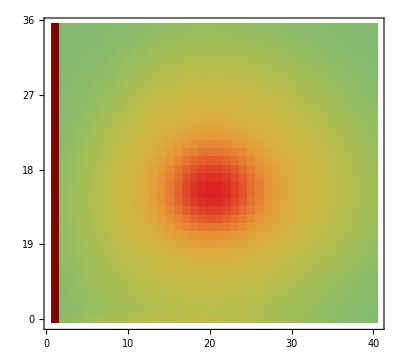

```mathematica
v=Reverse[Outer[Times,v1n,v1m]+Outer[Times,v2n,v2m]];
MatrixPlot[v,ColorFunction->"Rainbow",FrameStyle->Black,FrameTicks->{{{36,0},{27,19},{18,18},{9,27},{0,36}},{{0,0},{10,10},{20,20},{30,30},{40,40}}}]
```